## 2 eint matrix

```mathematica
basebox[L_,M_,P_,Q_,R_,S_,I_,x_,y_]:={EdgeForm[Thin],White,Rectangle[{x,y}],
Black,
Text[L,{.25+x,(3/4+1/8)+y}],Text[M,{.75+x,(3/4+1/8)+y}],
Text[P,{.25+x,(2/4+1/8)+y}],Text[Q,{.75+x,(2/4+1/8)+y}],
Text[R,{.25+x,(1/4+1/8)+y}],Text[S,{.75+x,(1/4+1/8)+y}],
Text[I,{.50+x,(0/4+1/8)+y}]}
```

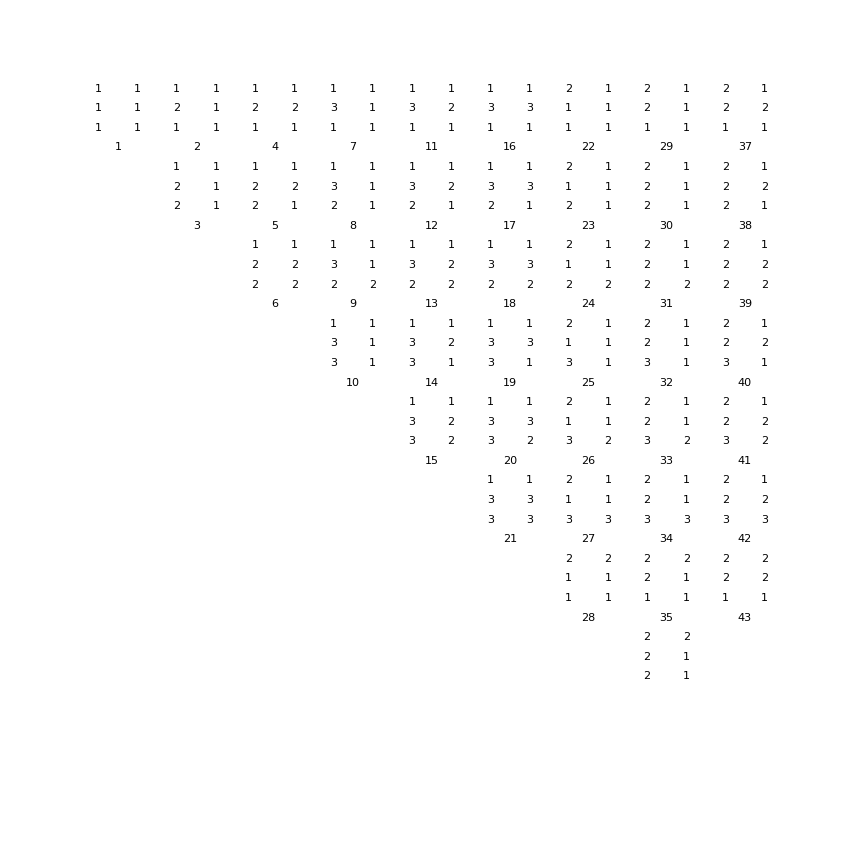

```mathematica
Graphics[{basebox[1,1,1,1,1,1,1,0,0],basebox[1,1,2,1,1,1,2,1,0],basebox[1,1,2,2,1,1,4,2,0],basebox[1,1,3,1,1,1,7,3,0],basebox[1,1,3,2,1,1,11,4,0],basebox[1,1,3,3,1,1,16,5,0],
basebox[2,1,1,1,1,1,22,6,0],basebox[2,1,2,1,1,1,29,7,0],basebox[2,1,2,2,1,1,37,8,0],
basebox[1,1,2,1,2,1,3,1,-1],basebox[1,1,2,2,2,1,5,2,-1],basebox[1,1,3,1,2,1,8,3,-1],basebox[1,1,3,2,2,1,12,4,-1],basebox[1,1,3,3,2,1,17,5,-1],basebox[2,1,1,1,2,1,23,6,-1],basebox[2,1,2,1,2,1,30,7,-1],basebox[2,1,2,2,2,1,38,8,-1],
basebox[1,1,2,2,2,2,6,2,-2],basebox[1,1,3,1,2,2,9,3,-2],basebox[1,1,3,2,2,2,13,4,-2],basebox[1,1,3,3,2,2,18,5,-2],basebox[2,1,1,1,2,2,24,6,-2],basebox[2,1,2,1,2,2,31,7,-2],basebox[2,1,2,2,2,2,39,8,-2],
basebox[1,1,3,1,3,1,10,3,-3],basebox[1,1,3,2,3,1,14,4,-3],basebox[1,1,3,3,3,1,19,5,-3],basebox[2,1,1,1,3,1,25,6,-3],basebox[2,1,2,1,3,1,32,7,-3],basebox[2,1,2,2,3,1,40,8,-3],
basebox[1,1,3,2,3,2,15,4,-4],basebox[1,1,3,3,3,2,20,5,-4],basebox[2,1,1,1,3,2,26,6,-4],basebox[2,1,2,1,3,2,33,7,-4],basebox[2,1,2,2,3,2,41,8,-4],
basebox[1,1,3,3,3,3,21,5,-5],basebox[2,1,1,1,3,3,27,6,-5],basebox[2,1,2,1,3,3,34,7,-5],basebox[2,1,2,2,3,3,42,8,-5],
basebox[2,2,1,1,1,1,28,6,-6],basebox[2,2,2,1,1,1,35,7,-6],basebox[2,2,2,2,1,1,43,8,-6],
basebox[2,2,2,1,2,1,36,7,-7],basebox[2,2,2,2,2,1,44,8,-7],
basebox[2,2,2,2,2,2,45,8,-8], basebox["L","M","P","Q","R","S","I",0,-8]}]
```

## Profiling info

```mathematica
(*all times are in ms unless otherwise noted*)
n2eints={
74305,
353220,
1081185,
2588950,
5299140,
9726255,
16476670,
26248635
};
eint2gpuT={
4.6821,
18.056,
52.512,
118.2,
237.96,
437.88,
730.24,
1159.98
}; (*millisecs*)
lmpqrsArrayT={
0.18406,
0.71441,
2.2137,
5.3615,
11.076,
20.818,
35.962,
57.998
};
eint2cpuT={
59.9956,
320.001,
980,
2360,
4910,
8880,
15140,
24180
};(*millisecs*)
formpqCpuIter={
21,
19,
19,
19,
19,
24,
26,
24
};
formpqCpuT={
39.997,
110,
350,
750,
1540,
3660,
6930,
10230
};(*total time per run*)
cpuTotalT={
0.124,
0.493,
1.443,
3.38,
6.786,
13.298,
23.234,
35.634
};(*time in s*)
formpqGpuOldIter={
21,
19,
19,
19,
19,
19,
19,
19
};
formpqGpuOldT={
2.9464,
7.5634,
15.349,
26.32,
39.457,
88.785,
135.64,
193.99
};(*time per iter*)
GpuTotalOldT={
0.782,
1.07,
1.518,
2.081,
2.722,
4.148,
5.579,
7.471
};(*time in s*)
formpqGpuNewIter={
21,
19,
19,
19,
19,
19,
19,
19
};
formpqGpuNewT={
6.0693,
14.25,
27.819,
53.952,
96.135,
173.64,
291.79,
459.38
};(*time per iter*)
GpuTotalNewT={
0.842,
1.196,
1.757,
2.587,
3.804,
5.779,
8.608,
12.593
};(*time in s*)
```

```mathematica
Transpose[{n2eints, eint2gpuT}]
```

{{74305,4.6821},{353220,18.056},{1081185,52.512},{2588950,118.2},{5299140,237.96},{9726255,437.88},{16476670,730.24},{26248635,1159.98}}

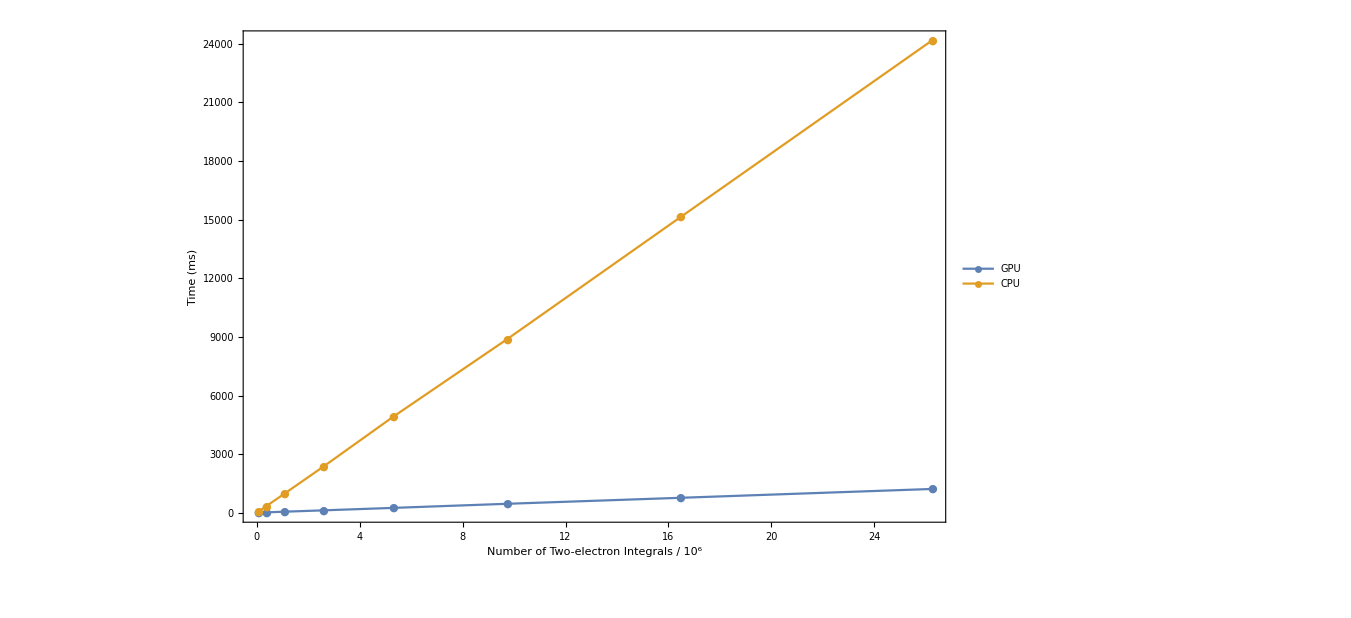

```mathematica
(*2eint*)ListLinePlot[{Transpose[{n2eints/10^6, (eint2gpuT + lmpqrsArrayT)}],Transpose[{n2eints/10^6, eint2cpuT}]}, Frame->True,FrameLabel->{"Number of Two-electron Integrals / 10^6", "Time (ms)"},ImageSize->1000,BaseStyle->{FontSize->15},LabelStyle->Black,PlotLegends->Placed[{"GPU","CPU"},{0.85,0.5}],PlotMarkers->"●"]
```

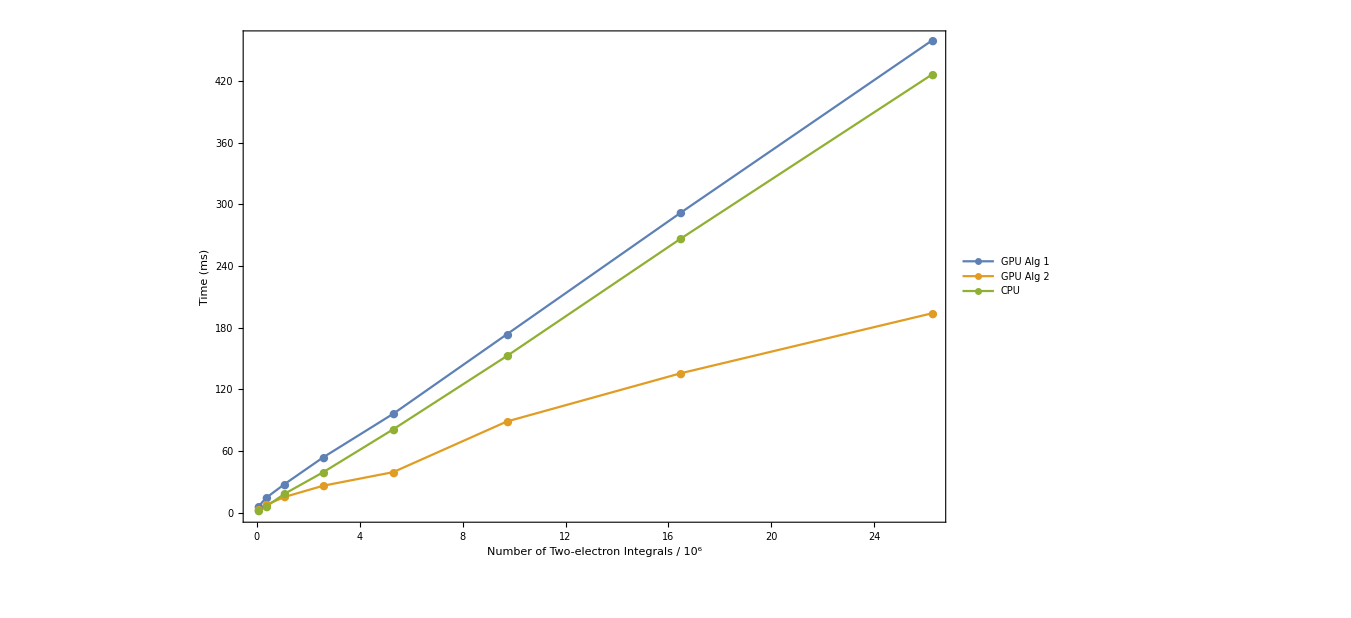

```mathematica
(*Formpq algs*)ListLinePlot[{Transpose[{n2eints/10^6, formpqGpuNewT}],Transpose[{n2eints/10^6, formpqGpuOldT}],Transpose[{n2eints/10^6, formpqCpuT/formpqCpuIter}]}, Frame->True,FrameLabel->{"Number of Two-electron Integrals / 10^6", "Time (ms)"},ImageSize->1000,BaseStyle->{FontSize->15},LabelStyle->Black,PlotLegends->Placed[{"GPU Alg 1","GPU Alg 2","CPU"},{0.85,0.5}],PlotMarkers->"●"]
```

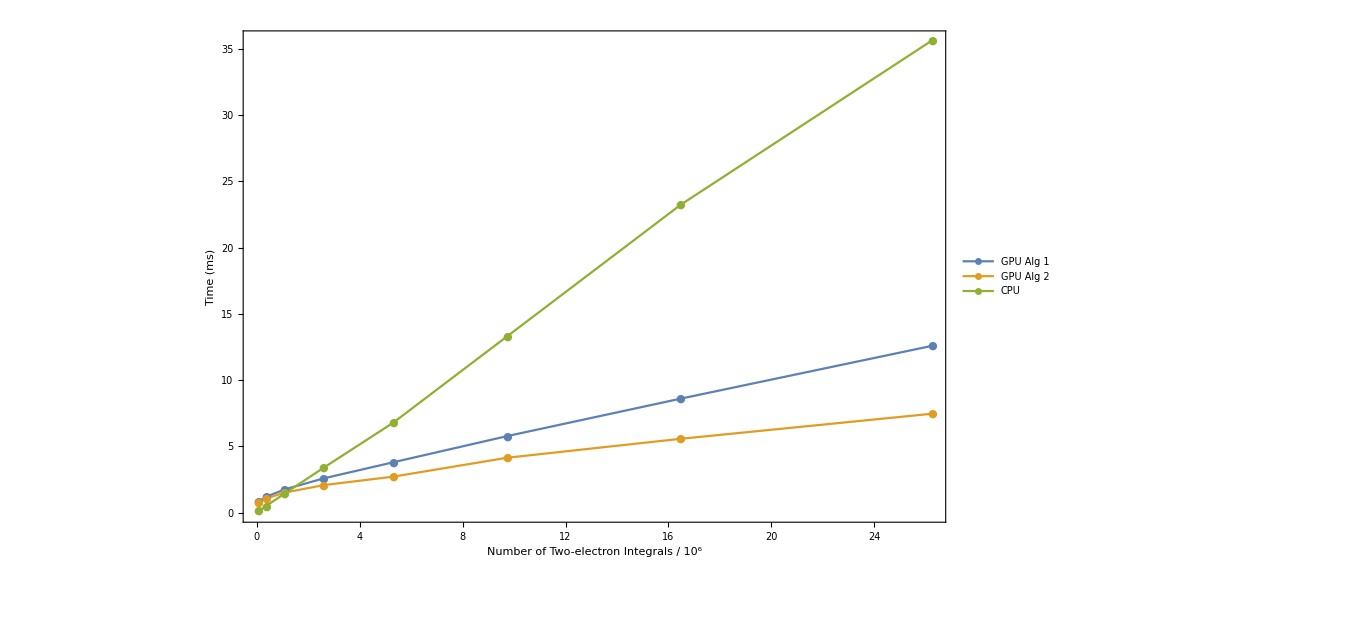

```mathematica
(*total time*)ListLinePlot[{Transpose[{n2eints/10^6, GpuTotalNewT}],Transpose[{n2eints/10^6, GpuTotalOldT}],Transpose[{n2eints/10^6, cpuTotalT}]}, Frame->True,FrameLabel->{"Number of Two-electron Integrals / 10^6", "Time (ms)"},ImageSize->1000,BaseStyle->{FontSize->15},LabelStyle->Black,PlotLegends->Placed[{"GPU Alg 1","GPU Alg 2","CPU"},{0.85,0.5}],PlotMarkers->"●",PlotRange->All]
```